```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"M1LC"}]];
DirsMG=Select[FileNames[],StringContainsQ[#,"GFP"]==True&];
DirsMG=SortBy[DirsMG,ToExpression@StringTake[#,{18,First@First@StringPosition[#,".csv"]-1}]&];
DirsMR=Select[FileNames[],StringContainsQ[#,"RFP"]==True&];
DirsMR=SortBy[DirsMR,ToExpression@StringTake[#,{18,First@First@StringPosition[#,".csv"]-1}]&];
GFPMnum=Import[FileNameJoin[{NotebookDirectory[],"usedcellNO","usedcellNO-M1LC.csv"}]];
GFPM=Flatten[Table[Import[FileNameJoin[{NotebookDirectory[],"M1LC",DirsMG[[i]]}]][[GFPMnum[[i]]]],{i,1,Length@DirsMG}],1];
RFPMnum=Import[FileNameJoin[{NotebookDirectory[],"usedcellNOR","usedcellNOR-M1LC.csv"}]];
RFPM=Flatten[Table[Import[FileNameJoin[{NotebookDirectory[],"M1LC",DirsMR[[i]]}]][[RFPMnum[[i]]]],{i,1,Length@DirsMR}],1];

SetDirectory[FileNameJoin[{NotebookDirectory[],"M3LC"}]];
DirsMG=Select[FileNames[],StringContainsQ[#,"GFP"]==True&];
DirsMG=SortBy[DirsMG,ToExpression@StringTake[#,{18,First@First@StringPosition[#,".csv"]-1}]&];
DirsMR=Select[FileNames[],StringContainsQ[#,"RFP"]==True&];
DirsMR=SortBy[DirsMR,ToExpression@StringTake[#,{18,First@First@StringPosition[#,".csv"]-1}]&];
GFPMnum=Import[FileNameJoin[{NotebookDirectory[],"usedcellNO","usedcellNO-M3LC.csv"}]];
GFPM=Join[GFPM,Flatten[Table[Import[FileNameJoin[{NotebookDirectory[],"M3LC",DirsMG[[i]]}]][[GFPMnum[[i]]]],{i,1,Length@DirsMG}],1]];
RFPMnum=Import[FileNameJoin[{NotebookDirectory[],"usedcellNOR","usedcellNOR-M3LC.csv"}]];
RFPM=Join[RFPM,Flatten[Table[Import[FileNameJoin[{NotebookDirectory[],"M3LC",DirsMR[[i]]}]][[RFPMnum[[i]]]],{i,1,Length@DirsMR}],1]];

SetDirectory[FileNameJoin[{NotebookDirectory[],"NM1LC"}]];
DirsNMG=Select[FileNames[],StringContainsQ[#,"GFP"]==True&];
DirsNMG=SortBy[DirsNMG,ToExpression@StringTake[#,{18,First@First@StringPosition[#,".csv"]-1}]&];
DirsNMR=Select[FileNames[],StringContainsQ[#,"RFP"]==True&];
DirsNMR=SortBy[DirsNMR,ToExpression@StringTake[#,{18,First@First@StringPosition[#,".csv"]-1}]&];
GFPNMnum=Import[FileNameJoin[{NotebookDirectory[],"usedcellNO","usedcellNO-NM1LC.csv"}]];
GFPNM=Flatten[Table[Import[FileNameJoin[{NotebookDirectory[],"NM1LC",DirsNMG[[i]]}]][[GFPNMnum[[i]]]],{i,1,Length@DirsNMG}],1];
RFPNMnum=Import[FileNameJoin[{NotebookDirectory[],"usedcellNOR","usedcellNOR-NM1LC.csv"}]];
RFPNM=Flatten[Table[Import[FileNameJoin[{NotebookDirectory[],"NM1LC",DirsNMR[[i]]}]][[RFPNMnum[[i]]]],{i,1,Length@DirsNMR}],1];

SetDirectory[FileNameJoin[{NotebookDirectory[],"NM3LC"}]];
DirsNMG=Select[FileNames[],StringContainsQ[#,"GFP"]==True&];
DirsNMG=SortBy[DirsNMG,ToExpression@StringTake[#,{18,First@First@StringPosition[#,".csv"]-1}]&];
DirsNMR=Select[FileNames[],StringContainsQ[#,"RFP"]==True&];
DirsNMR=SortBy[DirsNMR,ToExpression@StringTake[#,{18,First@First@StringPosition[#,".csv"]-1}]&];
GFPNMnum=Import[FileNameJoin[{NotebookDirectory[],"usedcellNO","usedcellNO-NM3LC.csv"}]];
GFPNM=Join[GFPNM,Flatten[Table[Import[FileNameJoin[{NotebookDirectory[],"NM3LC",DirsNMG[[i]]}]][[GFPNMnum[[i]]]],{i,1,Length@DirsNMG}],1]];
RFPNMnum=Import[FileNameJoin[{NotebookDirectory[],"usedcellNOR","usedcellNOR-NM3LC.csv"}]];
RFPNM=Join[RFPNM,Flatten[Table[Import[FileNameJoin[{NotebookDirectory[],"NM3LC",DirsNMR[[i]]}]][[RFPNMnum[[i]]]],{i,1,Length@DirsNMR}],1]];

SetDirectory[FileNameJoin[{NotebookDirectory[],"NM4LC"}]];
DirsNMG=Select[FileNames[],StringContainsQ[#,"GFP"]==True&];
DirsNMG=SortBy[DirsNMG,ToExpression@StringTake[#,{18,First@First@StringPosition[#,".csv"]-1}]&];
DirsNMR=Select[FileNames[],StringContainsQ[#,"RFP"]==True&];
DirsNMR=SortBy[DirsNMR,ToExpression@StringTake[#,{18,First@First@StringPosition[#,".csv"]-1}]&];
GFPNMnum=Import[FileNameJoin[{NotebookDirectory[],"usedcellNO","usedcellNO-NM4LC.csv"}]];
GFPNM=Join[GFPNM,Flatten[Table[Import[FileNameJoin[{NotebookDirectory[],"NM4LC",DirsNMG[[i]]}]][[GFPNMnum[[i]]]],{i,1,Length@DirsNMG}],1]];
RFPNMnum=Import[FileNameJoin[{NotebookDirectory[],"usedcellNOR","usedcellNOR-NM4LC.csv"}]];
RFPNM=Join[RFPNM,Flatten[Table[Import[FileNameJoin[{NotebookDirectory[],"NM4LC",DirsNMR[[i]]}]][[RFPNMnum[[i]]]],{i,1,Length@DirsNMR}],1]];

GFPNM=Transpose@Join[{GFPNM[[1;;-1,1]]-0.03},{GFPNM[[1;;-1,2]]}];
GFPNM=Select[GFPNM,#[[1]]>=0&&#[[1]]<1&];
GFPM=Transpose@Join[{(GFPM[[1;;-1,1]]-0.04)/1.},{GFPM[[1;;-1,2]]}];
GFPM=Select[GFPM,#[[1]]>=0&&#[[1]]<1&];
RFPNM=Transpose@Join[{RFPNM[[1;;-1,1]]-0.07},{RFPNM[[1;;-1,2]]}];
RFPNM=Select[RFPNM,#[[1]]>=0&&#[[1]]<1&];
RFPM=Transpose@Join[{RFPM[[1;;-1,1]]-0.03},{RFPM[[1;;-1,2]]}];
RFPM=Select[RFPM,#[[1]]>=0&&#[[1]]<1&];
Length@GFPNM
Length@GFPM
Length@RFPNM
Length@RFPM
```

8377

16162

4689

5654

```mathematica
(* ===1. 输入你的数据===*)
MSIs[dataA_,dataB_]:=Module[{},(* ===2. 加上组别变量 Group：A=0,B=1===*)
dataAWithGroup=dataA/. {x_,y_}:>{x,0,y};
dataBWithGroup=dataB/. {x_,y_}:>{x,1,y};

(*合并成一个总数据集：每行是 {x,Group,y}*)
allData=Join[dataAWithGroup,dataBWithGroup];

(* ===3. 构建带交互项的线性模型：y~x+Group+x*Group===*)
lmFull=LinearModelFit[allData,{x,g,x*g},(*自变量：x，组别 g，以及交互项 x*g*){x,g} (*声明自变量的符号*)];

(*看一下模型结果（可选）*)
lmFull["ParameterTable"];
lmFull["AdjustedRSquared"];

(* ===4. 看“斜率是否相同”：检验交互项 x*g 的显著性===*)

(*找出交互项 x*g 对应这一行,这一行里面通常包含：估计值、标准误、t统计量、p值等。看这里的 p 值：-p<0.05：认为两组斜率不同（不共用一条线）-p>=0.05：不能拒绝“斜率相同”这个假设*)

(* ===5. 如果斜率相同，再检验截距是否相同：Group 主效应 g 的显著性，groupRow 中的 p 值：-p<0.05：两组在 y 方向上有显著平移（截距不同）-p>=0.05：截距也可以认为相同，两组基本一条线*)

lmNoX=LinearModelFit[allData,{g},(*只用组别作为自变量*){x,g},(*数据里有 x 和 g，但这里 x 不参与回归，只作为“存在的变量”*)NominalVariables->g];
lmNoX["AdjustedRSquared"];

(*残差平方和 SSE*)sseFull=Total[(lmFull["FitResiduals"])^2];
sseNoX=Total[(lmNoX["FitResiduals"])^2];

(*x 在控制组别 G 后的部分 R^2*)
partialR2X=(sseNoX-sseFull)/sseNoX//N;
Print[partialR2X];
Print[lmFull["ParameterTable"]];
];

(*清理符号*)Clear[ChowTest1D];
(*ChowTest1D[data1,data2,α] data1,data2:形如 {{x1,y1},{x2,y2},...} 的两组数据 α:显著性水平（例如 0.05），可选，默认 0.05*)
ChowTest1D[data1_List,data2_List,α_:0.05]:=Module[{k=2,(*参数个数：截距+斜率*)lmAll,lm1,lm2,(*三个模型*)ssep,sse1,sse2,(*SSE*)n1,n2,df1,df2,(*自由度*)f,p},(*拟合整体模型& 分组模型*)lmAll=LinearModelFit[Join[data1,data2],x,x];
lm1=LinearModelFit[data1,x,x];
lm2=LinearModelFit[data2,x,x];
(*残差平方和*)ssep=Total[lmAll["FitResiduals"]^2];
sse1=Total[lm1["FitResiduals"]^2];
sse2=Total[lm2["FitResiduals"]^2];
(*样本量& 自由度*)n1=Length[data1];
n2=Length[data2];
df1=k;
df2=n1+n2-2 k;
(*Chow F 统计量*)f=((ssep-(sse1+sse2))/df1)/((sse1+sse2)/df2);
(*p 值*)p=1-CDF[FRatioDistribution[df1,df2],f];
<|"FStatistic"->f,"pValue"->p,"DegreesOfFreedom1"->df1,"DegreesOfFreedom2"->df2,"Alpha"->α,"RejectH0Q"->(p<α) (*True 则拒绝“同一回归模型”的原假设*)|>];
```

```mathematica
hisx=Histogram[{Flatten@Take[GFPNM,All,{1}],Flatten@Take[GFPM,All,{1}]},50,"Probability",ChartStyle->{RGBColor[127/255,142/255,212/255],RGBColor[251/255,190/255,83/255]},Axes->False,Frame->True,PlotRange->{{0.015,0.98},{0,0.12}},FrameTicksStyle->Directive[Black,28],FrameStyle->Directive[Black,Thickness[0.0075]],FrameTicks->{{{#,#,{0.02,0}}&/@Range[0,0.12,0.06],None},{{#,#,{0.02,0}}&/@Range[0,1,0.2],None}},ImageSize->800,AspectRatio->0.25];
hisy=Histogram[{Flatten@Take[GFPNM,All,{2}],Flatten@Take[GFPM,All,{2}]},50,"Probability",ChartStyle->{RGBColor[127/255,142/255,212/255],RGBColor[251/255,190/255,83/255]},BarOrigin->Right,Frame->True,PlotRange->{{0,0.3},{0.015,0.98}},FrameTicksStyle->Directive[Black,28],FrameStyle->Directive[Black,Thickness[0.025]],FrameTicks->{{{#,#,{0.02,0}}&/@Range[0,1,0.2],None},{{#,#,{0.02,0}}&/@Range[0,0.3,0.1],None}},ImageSize->200,AspectRatio->3.5];
trpx=Histogram[{Flatten@Take[RFPNM,All,{1}],Flatten@Take[GFPM,All,{1}]},50,"Probability",ChartStyle->{RGBColor[127/255,142/255,212/255],RGBColor[251/255,190/255,83/255]},Axes->False,Frame->True,PlotRange->{{0.015,0.98},{0,0.16}},FrameTicksStyle->Directive[Black,28],FrameStyle->Directive[Black,Thickness[0.0075]],FrameTicks->{{{#,#,{0.02,0}}&/@Range[0,0.16,0.08],None},{{#,#,{0.02,0}}&/@Range[0,1,0.2],None}},ImageSize->800,AspectRatio->0.25];
trpy=Histogram[{Flatten@Take[RFPNM,All,{2}],Flatten@Take[GFPM,All,{2}]},50,"Probability",ChartStyle->{RGBColor[127/255,142/255,212/255],RGBColor[251/255,190/255,83/255]},BarOrigin->Right,Frame->True,PlotRange->{{0,0.7},{0.015,0.98}},FrameTicksStyle->Directive[Black,28],FrameStyle->Directive[Black,Thickness[0.025]],FrameTicks->{{{#,#,{0.02,0}}&/@Range[0,1,0.2],None},{{#,#,{0.02,0}}&/@Range[0,0.6,0.3],None}},ImageSize->200,AspectRatio->3.5];
```

FittedModel[…]

0.524726

FittedModel[…]

0.680464

General::munfl: Exp[-6015.66] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::munfl: Exp[-4782.51] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

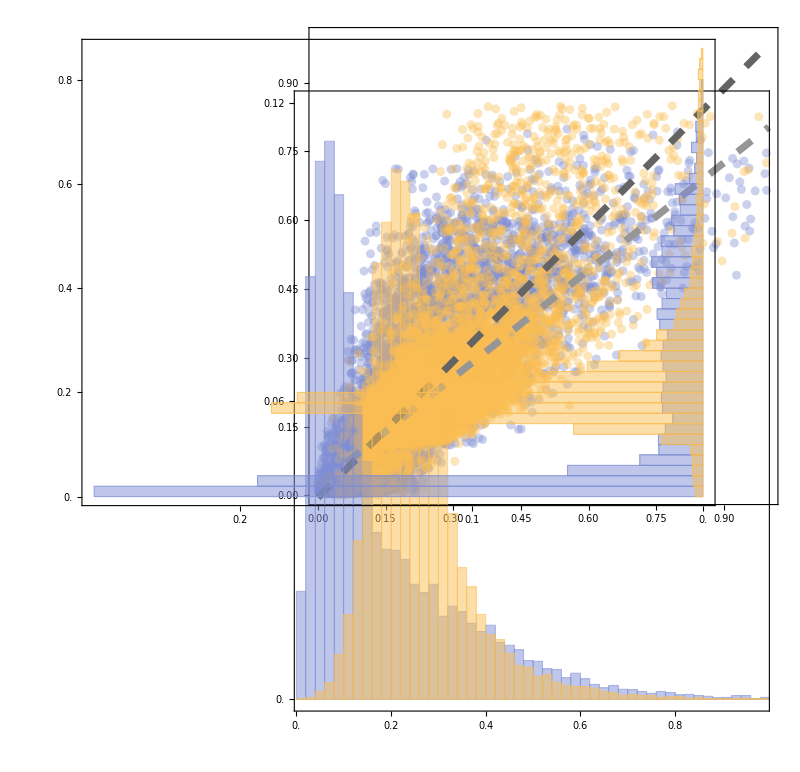

0.880773

<|FStatistic→381.41,pValue→0.,DegreesOfFreedom1→2,DegreesOfFreedom2→24535,Alpha→0.05,RejectH0Q→True|>

General::munfl: Exp[-9157.14] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

0.620938

General::munfl: Exp[-9157.14] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.00495345 | 0.00145311 | -3.40886 | 0.000653386
x | 0.990176 | 0.00600372 | 164.927 | 0.
g | 0.0274277 | 0.00237426 | 11.5521 | 8.65485×10^-31
g x | -0.209397 | 0.00910909 | -22.9877 | 1.03486×10^-115

```mathematica
fitdata=Join[GFPM,GFPNM];
fit1=LinearModelFit[GFPM,x,x]
fit1["AdjustedRSquared"]
fit2=LinearModelFit[GFPNM,x,x]
fit2["AdjustedRSquared"]
fit=LinearModelFit[fitdata,x,x];
fit["AdjustedRSquared"];
fit1["ParameterTableEntries"];
fit2["ParameterTableEntries"];
fithis=Show[ListPlot[{GFPNM,GFPM},PlotStyle->{{RGBColor[127/255,142/255,212/255],PointSize[0.01],Opacity[0.4]},{RGBColor[251/255,190/255,83/255],PointSize[0.01],Opacity[0.4]}},Frame->True,PlotRange->{{0,1},{0,1}},FrameTicksStyle->Directive[Black,28],FrameStyle->Directive[Black,Thickness[0.008]],ImageSize->643,AspectRatio->1],
Plot[fit1[x],{x,0,1},PlotStyle->{Dashing[0.02],Thickness[0.008],RGBColor[150/255,150/255,150/255]},ImageSize->Large],
Plot[fit2[x],{x,0,1},PlotStyle->{Dashing[0.02],Thickness[0.008],RGBColor[100/255,100/255,100/255]},ImageSize->Large]
];
fithis=Graphics[{Rectangle[{0,0},{2,2},fithis],Rectangle[{-0.056,-0.8},{1.97,1.8},hisx],Rectangle[{-0.9,0},{1.8,1.955},hisy]},ImageSize->800]
Export[FileNameJoin[{NotebookDirectory[],"plot","fithis-LC.eps"}],fithis];

paramsA=fit2["BestFitParameters"];  (*{aA,bA}：截距、斜率*)
paramsB=fit1["BestFitParameters"];  (*{aB,bB}*)

aA=paramsA[[1]];
bA=paramsA[[2]];
aB=paramsB[[1]];
bB=paramsB[[2]];
distance=Sqrt[(aA-aB)^2+(bA-bB)^2]//N;
normA=Sqrt[aA^2+bA^2];
normB=Sqrt[aB^2+bB^2];
normDiff=Sqrt[(aA-aB)^2+(bA-bB)^2];

MSI=1-normDiff/(normA+normB)//N
ChowTest1D[GFPM,GFPNM,0.05]
MSIs[GFPNM,GFPM]
```

```mathematica
(*在控制实验组别差异后，x 仍能解释约 62% 的剩余 y 变异，说明 x 在两组实验中对 y 的变化有很强的解释能力，尽管两组之间的线性关系并不完全相同。*)
```

0.58232

0.674082

General::munfl: Exp[-2471.99] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

{{-0.0328293,0.00263208,-12.4728,3.04907×10^-35},{0.836676,0.0094239,88.7823,0.}}

General::munfl: Exp[-2632.08] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

{{-0.0423887,0.0011437,-37.0627,6.28335×10^-264},{0.852791,0.00866012,98.4734,0.}}

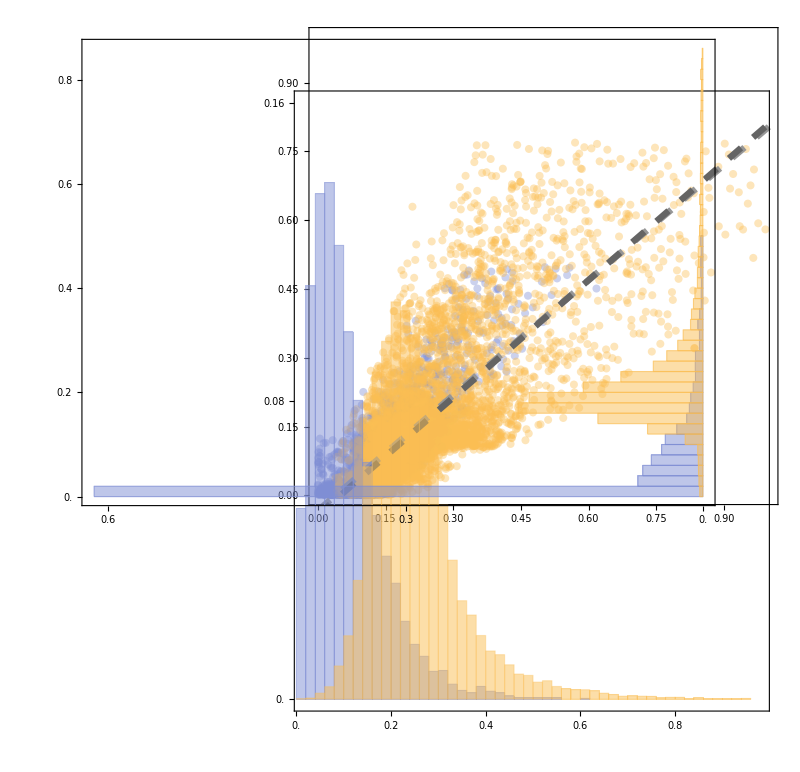

0.988921

<|FStatistic→8.72293,pValue→0.00016401,DegreesOfFreedom1→2,DegreesOfFreedom2→10339,Alpha→0.05,RejectH0Q→True|>

General::munfl: Exp[-1360.86] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

0.598783

General::munfl: Exp[-1360.86] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.0423887 | 0.00202186 | -20.9652 | 1.30755×10^-95
x | 0.852791 | 0.0153095 | 55.7034 | 0.
g | 0.00955937 | 0.00291851 | 3.27542 | 0.00105851
g x | -0.0161152 | 0.0170636 | -0.944418 | 0.344978

```mathematica
fitdata=Join[RFPM,RFPNM];
fit1=LinearModelFit[RFPM,x,x];
fit1["AdjustedRSquared"]
fit2=LinearModelFit[RFPNM,x,x];
fit2["AdjustedRSquared"]
fit=LinearModelFit[fitdata,x,x];
fit["AdjustedRSquared"];
fit1["ParameterTableEntries"]
fit2["ParameterTableEntries"]
fittrp=Show[ListPlot[{RFPNM,RFPM},PlotStyle->{{RGBColor[127/255,142/255,212/255],PointSize[0.01],Opacity[0.4]},{RGBColor[251/255,190/255,83/255],PointSize[0.01],Opacity[0.4]}},Frame->True,PlotRange->{{0,1},{0,1}},FrameTicksStyle->Directive[Black,28],FrameStyle->Directive[Black,Thickness[0.008]],ImageSize->Large,AspectRatio->1],Plot[fit1[x],{x,0,1},PlotStyle->{Dashing[0.02],Thickness[0.008],RGBColor[150/255,150/255,150/255]},ImageSize->Large],
Plot[fit2[x],{x,0,1},PlotStyle->{Dashing[0.02],Thickness[0.008],RGBColor[100/255,100/255,100/255]},ImageSize->Large]];
fittrp=Graphics[{Rectangle[{0,0},{2,2},fittrp],Rectangle[{-0.056,-0.8},{1.97,1.8},trpx],Rectangle[{-0.9,0},{1.8,1.955},trpy]},ImageSize->800]
Export[FileNameJoin[{NotebookDirectory[],"plot","fittrp-LC.eps"}],fittrp];

paramsA=fit2["BestFitParameters"];  (*{aA,bA}：截距、斜率*)
paramsB=fit1["BestFitParameters"];  (*{aB,bB}*)

aA=paramsA[[1]];
bA=paramsA[[2]];
aB=paramsB[[1]];
bB=paramsB[[2]];
distance=Sqrt[(aA-aB)^2+(bA-bB)^2]//N;
normA=Sqrt[aA^2+bA^2];
normB=Sqrt[aB^2+bB^2];
normDiff=Sqrt[(aA-aB)^2+(bA-bB)^2];

MSI=1-normDiff/(normA+normB)//N(*两组对 x 的响应趋势相似。*)
ChowTest1D[RFPM,RFPNM,0.05]
MSIs[RFPNM,RFPM]
```

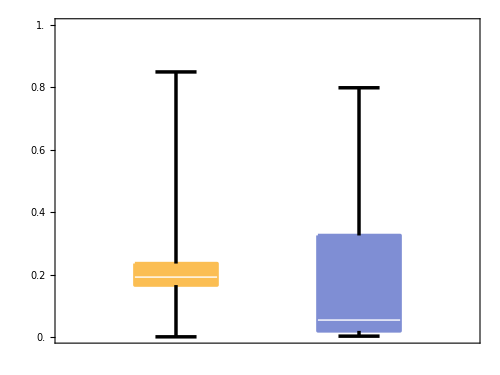

TTest::nortst: {0,0} 中至少有一个通过正态性检验得到的 p 值低于 0.025. {T} 中的检验要求数据服从正态分布.

8.71204×10^-95

```mathematica
Grodata=Join[{Flatten@Take[GFPM,All,{2}]},{Flatten@Take[GFPNM,All,{2}]}];
Gromeanplot=BoxWhiskerChart[Grodata,{{"Whiskers",Thickness[0.005]},{"Fences",Thickness[0.005]}},ChartBaseStyle->EdgeForm[Thickness[0.005]],PlotRange->{0,1},ChartStyle->{RGBColor[251/255,190/255,83/255],RGBColor[127/255,142/255,212/255]},FrameStyle->Directive[Thickness[0.008],30,Black],FrameTicks->{{{#,#,{0.02,0}}&/@Range[0,1,0.2],None},{{None,None}}},AspectRatio->0.75,ImageSize->500]
TTest[Grodata]
```

```mathematica
lcMlist={"M1LC","M3LC"};
lcNMlist={"NM1LC","NM3LC","NM4LC"};
compare1={lcMlist,lcNMlist};
```

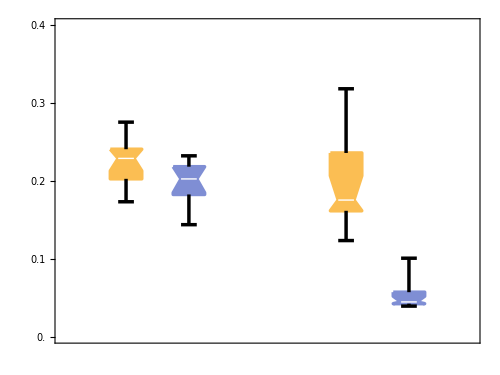

0.0409863

TTest::nortst: {0.142203,0.00679012} 中至少有一个通过正态性检验得到的 p 值低于 0.025. {T} 中的检验要求数据服从正态分布.

9.39457×10^-8

```mathematica
compare=compare1;
gromotileG={};
stdmotileG={};
gromotileR={};
stdmotileR={};
Do[
SetDirectory[FileNameJoin[{NotebookDirectory[],compare1[[1,j]]}]];
DirsM=FileNames[];
DirsM={Select[DirsM,StringContainsQ[#,"GFP"]==True&],Select[DirsM,StringContainsQ[#,"RFP"]==True&]};
Do[
growthrateG=Import[FileNameJoin[{NotebookDirectory[],compare1[[1,j]],DirsM[[1,i]]}]];
growthrateG=Flatten@Take[growthrateG,All,{2}];
growthrateR=Import[FileNameJoin[{NotebookDirectory[],compare1[[1,j]],DirsM[[2,i]]}]];
growthrateR=Flatten@Take[growthrateR,All,{2}];
growthratelist=Join[growthrateG,growthrateR];
MeangroG=Mean@growthrateG;
stdgroG=StandardDeviation@growthrateG;
MeangroR=Mean@growthrateR;
stdgroR=StandardDeviation@growthrateR;
gromotileG=Join[gromotileG,{MeangroG}];
stdmotileG=Join[stdmotileG,{stdgroG}];
gromotileR=Join[gromotileR,{MeangroR}];
stdmotileR=Join[stdmotileR,{stdgroR}];
,{i,1,Length@DirsM[[1]]}];
,{j,1,Length@compare1[[1]]}];

grononmotileG={};
stdnonmotileG={};
grononmotileR={};
stdnonmotileR={};
Do[
SetDirectory[FileNameJoin[{NotebookDirectory[],compare1[[2,j]]}]];
DirsNM=FileNames[];
DirsNM={Select[DirsNM,StringContainsQ[#,"GFP"]==True&],Select[DirsNM,StringContainsQ[#,"RFP"]==True&]};
Do[
growthrateG=Import[FileNameJoin[{NotebookDirectory[],compare1[[2,j]],DirsNM[[1,i]]}]];
growthrateG=Flatten@Take[growthrateG,All,{2}];
growthrateR=Import[FileNameJoin[{NotebookDirectory[],compare1[[2,j]],DirsNM[[2,i]]}]];
growthrateR=Flatten@Take[growthrateR,All,{2}];
growthratelist=Join[growthrateG,growthrateR];
MeangroG=Mean@growthrateG;
stdgroG=StandardDeviation@growthrateG;
MeangroR=Mean@growthrateR;
stdgroR=StandardDeviation@growthrateR;
grononmotileG=Join[grononmotileG,{MeangroG}];
stdnonmotileG=Join[stdnonmotileG,{stdgroG}];
grononmotileR=Join[grononmotileR,{MeangroR}];
stdnonmotileR=Join[stdnonmotileR,{stdgroR}];
,{i,1,Length@DirsNM[[1]]}];
,{j,1,Length@compare1[[1]]}];
GromeanplotG=BoxWhiskerChart[Join[{gromotileG},{grononmotileG}],{"Notched",{"Whiskers",Thickness[0.005]},{"Fences",Thickness[0.005]}},ChartBaseStyle->EdgeForm[Thickness[0.005]],PlotRange->{0,0.4},ChartStyle->{RGBColor[251/255,190/255,83/255],RGBColor[127/255,142/255,212/255]},FrameStyle->Directive[Thickness[0.008],30,Black],FrameTicks->{{{#,#,{0.02,0}}&/@Range[0,0.4,0.1],None},{{None,None}}},AspectRatio->0.75,ImageSize->500];
GromeanplotR=BoxWhiskerChart[Join[{gromotileR},{grononmotileR}],{"Notched",{"Whiskers",Thickness[0.005]},{"Fences",Thickness[0.005]}},ChartBaseStyle->EdgeForm[Thickness[0.005]],PlotRange->{0,0.4},ChartStyle->{RGBColor[251/255,190/255,83/255],RGBColor[127/255,142/255,212/255]},FrameStyle->Directive[Thickness[0.008],30,Black],FrameTicks->{{{#,#,{0.02,0}}&/@Range[0,0.4,0.1],None},{{None,None}}},AspectRatio->0.75,ImageSize->500];
Gromeanplot=BoxWhiskerChart[{{gromotileG,grononmotileG},{gromotileR,grononmotileR}},{"Notched",{"Whiskers",Thickness[0.005]},{"Fences",Thickness[0.005]}},ChartBaseStyle->EdgeForm[Thickness[0.005]],PlotRange->{0,0.4},ChartStyle->{RGBColor[251/255,190/255,83/255],RGBColor[127/255,142/255,212/255]},FrameStyle->Directive[Thickness[0.008],30,Black],FrameTicks->{{{#,#,{0.02,0}}&/@Range[0,0.4,0.1],None},{{None,None}}},AspectRatio->0.75,ImageSize->500,BarSpacing->{1,2}]
TTest[{gromotileG,grononmotileG}]
TTest[{gromotileR,grononmotileR}]
Export[FileNameJoin[{NotebookDirectory[],"plot","Gromeanplot-LC.eps"}],Gromeanplot];
```